## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
```

/home/bazow/mercury/gpu-vh/mathematica

### constants

```mathematica
hbarc=0.197326938;
```

```mathematica
Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120 ;
sFac = eg+eq ;
```

### plot styles

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[2],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
```

## Equation of state

```mathematica
eosDir ="/rhic/rhic-trunk/src/main/resources/eos/wuppertal-budapest/";
```

```mathematica
eosDataRaw=Import[ParentDirectory[wd]<>eosDir<>"eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];
```

```mathematica
rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

### LogP LogEd

```mathematica
LogPLogEdInt = Interpolation[eosData[[All,{2,4}]]];
```

```mathematica
LogPLogEddata=Table[{x,LogPLogEdInt[x]},{x,-228.95,17.1,0.1}];
```

```mathematica
LogPLogEd[x_]=rationalPolyFit[LogPLogEddata,23,23]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(-6118.24-5687.25 x+20752.8 x^2-11989.5 x^3+6431.19 x^4-1887.79 x^5+5662.75 x^6+774.668 x^7+1583.48 x^8+564.488 x^9+72.6145 x^10-3.7088 x^11-2.18679 x^12-0.0831203 x^13+0.0412004 x^14+0.0066034 x^15+0.000617511 x^16+0.0000648284 x^17+4.77023×10^-6 x^18+9.71339×10^-8 x^19-2.66954×10^-9 x^20+2.23958×10^-10 x^21+1.09764×10^-11 x^22-4.00488×10^-13 x^23)/(7543.66+15151.8 x-8032.37 x^2+9482.31 x^3+3014.63 x^4+6373.66 x^5+1545.36 x^6+1844.9 x^7+611.426 x^8+71.1031 x^9-5.33762 x^10-2.21946 x^11-0.0493085 x^12+0.0443146 x^13+0.00675165 x^14+0.000653431 x^15+0.0000683581 x^16+4.77883×10^-6 x^17+9.07311×10^-8 x^18-2.37502×10^-9 x^19+2.38412×10^-10 x^20+1.03977×10^-11 x^21-4.00498×10^-13 x^22-1.32581×10^-20 x^23)

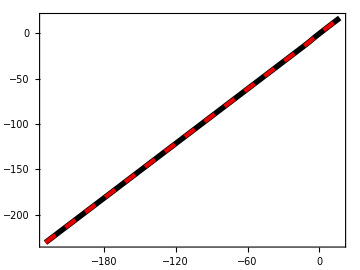

```mathematica
Plot[{LogPLogEdInt[x],LogPLogEd[x]},{x,-228.95,17.1}]
```

```mathematica
Max[Table[Abs[LogPLogEd[x]-LogPLogEdInt[x]],{x,-228.95,17.1,0.01}]]
```

0.000176269

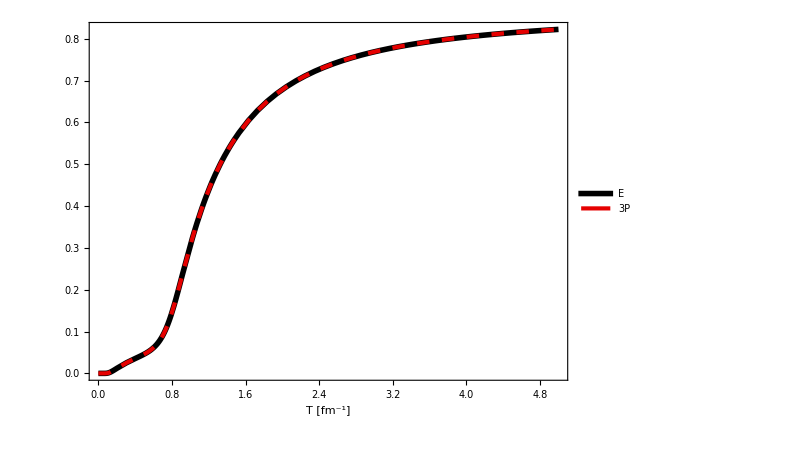

```mathematica
Plot[{PInt[T]/(sFac T^4/3),10^(LogPLogEd[Log[10,edInt[T]]])/(sFac T^4/3)},{T,.001,5},PlotStyle->styles,ImageSize->600,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75,PlotLegends->Placed[LineLegend[styles,{"E","3P"},LabelStyle-> {FontSize->14},LegendMarkerSize->{{45,4}}],{0.25,0.8}]]
```

```mathematica
Max[Table[Abs[10^(LogPLogEd[Log[10,edInt[T]]])/(sFac T^4/3)-PInt[T]/(sFac T^4/3)],{T,0.001,5,0.01}]]
```

0.0000246588

### cs2=dP/de(e)

```mathematica
LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];
```

```mathematica
dPdEdataE=Table[{edInt[T],dPIntE[edInt[T]]/dEIntE[edInt[T]]},{T,0.001,5,.01}];
```

```mathematica
LogdPdELogEddata=Table[{x,LogdPLogEdInt[x]/LogdELogEdInt[x]},{x,-228.95,17.1,0.1}];
```

```mathematica
dPdE[e_]=rationalPolyFit[dPdEdataE,13,13]/.{x->e}
```

(5.19193×10^-32+4.12361×10^-23 e+3.19559×10^-16 e^2+1.41704×10^-10 e^3+6.08714×10^-6 e^4+0.0296974 e^5+15.3826 e^6+460.649 e^7+1612.42 e^8+275.049 e^9+58.6028 e^10+6.50485 e^11+0.0300903 e^12+8.18943×10^-6 e^13)/(1.46379×10^-30+6.7166×10^-22 e+3.54777×10^-15 e^2+1.12256×10^-9 e^3+0.0000355178 e^4+0.136532 e^5+60.8577 e^6+1800.55 e^7+15190.2 e^8+590.257 e^9+293.991 e^10+21.4613 e^11+0.0930169 e^12+0.0000248109 e^13)

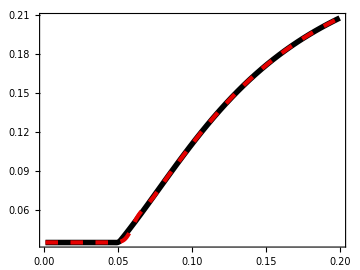

```mathematica
Plot[{dPIntE[edInt[T]]/dEIntE[edInt[T]],dPdE[edInt[T]]},{T,0.001,.2},PlotRange->All]
```

```mathematica
Max[Table[Abs[dPIntE[edInt[T]]/dEIntE[edInt[T]]-dPdE[edInt[T]]],{T,0.001,5,.01}]]
```

0.00030888

```mathematica
dPdE[e]//CForm
```

(5.191934309650155e-32 + 4.123605749683891e-23*e + 3.1955868410879504e-16*Power(e,2) + 1.4170364808063119e-10*Power(e,3) + 6.087136671592452e-6*Power(e,4) + 
     0.02969737949090831*Power(e,5) + 15.382615282179595*Power(e,6) + 460.6487249985994*Power(e,7) + 1612.4245252438795*Power(e,8) + 
     275.0492627924299*Power(e,9) + 58.60283714484669*Power(e,10) + 6.504847576502024*Power(e,11) + 0.03009027913262399*Power(e,12) + 
     8.189430244031285e-6*Power(e,13))/
   (1.4637868900982493e-30 + 6.716598285341542e-22*e + 3.5477700458515908e-15*Power(e,2) + 1.1225580509306008e-9*Power(e,3) + 
     0.00003551782901018317*Power(e,4) + 0.13653226327408863*Power(e,5) + 60.85769171450653*Power(e,6) + 1800.5461219450308*Power(e,7) + 
     15190.225535036281*Power(e,8) + 590.2572000057821*Power(e,9) + 293.99144775704605*Power(e,10) + 21.461303090563028*Power(e,11) + 
     0.09301685073435291*Power(e,12) + 0.000024810902623582917*Power(e,13))

### T(e)

```mathematica
LogTLogEDInt = Interpolation[eosData[[All,{2,1}]]];
TIntED[e_]=10^LogTLogEDInt[Log[10,e]];
```

```mathematica
TdataED=Table[{edInt[T],TIntED[edInt[T]]},{T,0.0001,5,0.01}];
```

```mathematica
Tint[e_]=rationalPolyFit[TdataED,11,11]/.{x->e}
```

(1.51007×10^-29+8.01406×10^-18 e+2.49548×10^-10 e^2+0.0000638104 e^3+0.487349 e^4+207.486 e^5+6686.07 e^6+14109.8 e^7+1471.62 e^8+14.0558 e^9+0.0154213 e^10+1.57805×10^-6 e^11)/(7.55867×10^-28+1.36864×10^-16 e+2.99813×10^-9 e^2+0.000503684 e^3+2.3169 e^4+578.078 e^5+11179.2 e^6+17965.7 e^7+1051.07 e^8+5.91631 e^9+0.00377834 e^10+1.84728×10^-7 e^11)

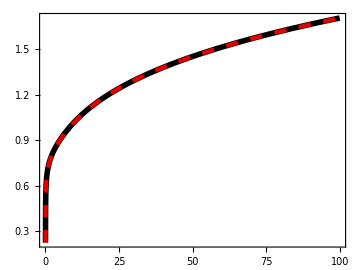

```mathematica
Plot[{TIntED[e],Tint[e]},{e,0.001,100}]
```

```mathematica
Max[Table[Abs[TIntED[e]-Tint[e]],{e,0.001,8254.11,0.1}]]
```

0.000920427

```mathematica
CForm[Tint[e]]
```

(1.510073201405604e-29 + 8.014062800678687e-18*e + 2.4954778310451065e-10*Power(e,2) + 0.000063810382643387*Power(e,3) + 0.4873490574161924*Power(e,4) + 
     207.48582344326206*Power(e,5) + 6686.07424325115*Power(e,6) + 14109.766109389702*Power(e,7) + 1471.6180520527757*Power(e,8) + 
     14.055788949565482*Power(e,9) + 0.015421252394182246*Power(e,10) + 1.5780479034557783e-6*Power(e,11))/
   (7.558667139355393e-28 + 1.3686372302041508e-16*e + 2.998130743142826e-9*Power(e,2) + 0.0005036835870305458*Power(e,3) + 2.316902328874072*Power(e,4) + 
     578.0778724946719*Power(e,5) + 11179.193315394154*Power(e,6) + 17965.67607192861*Power(e,7) + 1051.0730543534657*Power(e,8) + 
     5.916312075925817*Power(e,9) + 0.003778342768228011*Power(e,10) + 1.8472801679382593e-7*Power(e,11))

### e(T)

```mathematica
eddata=Table[{T,edInt[T]},{T,0.0001,5,0.1}];
```

```mathematica
ed[T_]=rationalPolyFit[eddata,23,23]/.{x->T}
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(-0.0119582+119.894 T-3156.95 T^2+32732.9 T^3-187900. T^4+712537. T^5-1.55705×10^6 T^6+1.48525×10^6 T^7+532133. T^8-1.9631×10^6 T^9-4484.45 T^10+1.79842×10^6 T^11+119345. T^12-1.34998×10^6 T^13-207838. T^14+654970. T^15-78643. T^16+40274. T^17+422620. T^18-409688. T^19-62005.8 T^20+46788.1 T^21+40784.3 T^22-12589.5 T^23)/(31630.1-127101. T+173528. T^2-39403.3 T^3-85582.6 T^4+9320.56 T^5+50882.7 T^6+20335.9 T^7-14897.7 T^8-23836.5 T^9-13726. T^10+4517.91 T^11+18056.2 T^12+14954.8 T^13+2569.62 T^14-9304.05 T^15-15606.4 T^16+8383.71 T^17+1591.32 T^18-678.748 T^19-33.5869 T^20+3.25206 T^21-0.196473 T^22+0.00544339 T^23)

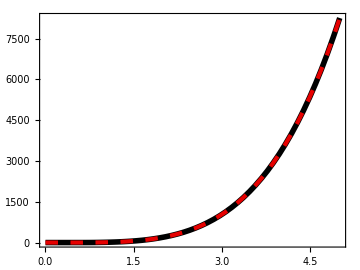

```mathematica
Plot[{edInt[T],ed[T]},{T,0.001,5}]
```

```mathematica
Max[Table[Abs[edInt[T]-ed[T]],{T,0.0001,5,0.1}]]
```

0.0000179524

## Plots

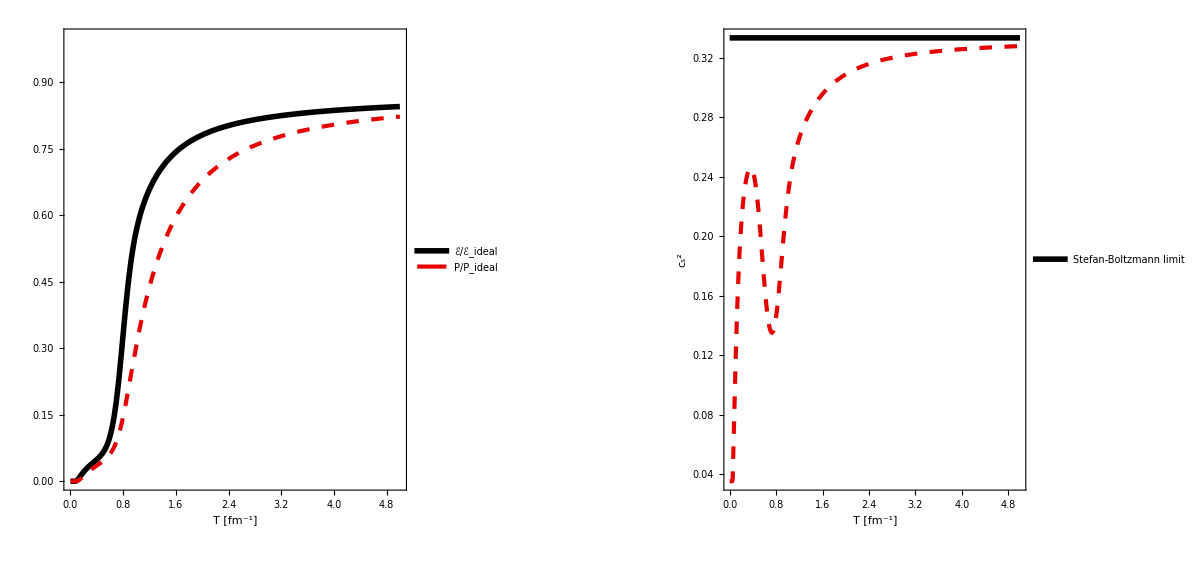

```mathematica
pPlot=Plot[{edInt[T]/(sFac T^4),10^(LogPLogEd[Log[10,edInt[T]]])/(sFac T^4/3)},{T,.001,5},PlotRange->{0,1},ImageSize->600,FrameLabel->{"T [fm^-1]",""},PlotLegends->Placed[LineLegend[styles,{"ℰ/ℰ_ideal","P/P_ideal"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.3}],ImagePadding->{{85,30},{80,20}}];
cs2Plot=Plot[{1/3,dPdE[edInt[T]]},{T,0.001,5},PlotRange->All,PlotLegends->Placed[LineLegend[styles,{"Stefan-Boltzmann limit"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.6,0.3}],ImageSize->600,FrameLabel->{"T [fm^-1]","c_s^2"},ImagePadding->{{85,30},{80,20}}];
eosGrid=GraphicsGrid[{{pPlot,cs2Plot}},ImageSize->1200]
```

```mathematica
Export[wd<>"/eosGrid.pdf",eosGrid]
```

/home/bazow/mercury/gpu-vh/mathematica/eosGrid.pdf

## Output for C

```mathematica
CForm[LogPLogEd[x]]
```

(-6118.240942492361 - 5687.251105195098*x + 20752.76275644727*Power(x,2) - 11989.517475674438*Power(x,3) + 6431.189740977292*Power(x,4) - 
     1887.7892172219235*Power(x,5) + 5662.745060345452*Power(x,6) + 774.6684795499582*Power(x,7) + 1583.4830157257804*Power(x,8) + 
     564.4875398887923*Power(x,9) + 72.61447772796548*Power(x,10) - 3.708800297832573*Power(x,11) - 2.1867927513752687*Power(x,12) - 
     0.08312033181718484*Power(x,13) + 0.04120042172447292*Power(x,14) + 0.006603398115960931*Power(x,15) + 0.0006175106780064349*Power(x,16) + 
     0.00006482843976373467*Power(x,17) + 4.770229269047069e-6*Power(x,18) + 9.71339211307907e-8*Power(x,19) - 2.6695366906807306e-9*Power(x,20) + 
     2.2395809810298253e-10*Power(x,21) + 1.0976424753178406e-11*Power(x,22) - 4.0048841416263433e-13*Power(x,23))/
   (7543.6556170684635 + 15151.776822013266*x - 8032.374892077859*Power(x,2) + 9482.306880935743*Power(x,3) + 3014.631292911099*Power(x,4) + 
     6373.655296404095*Power(x,5) + 1545.3557368707916*Power(x,6) + 1844.8983613169753*Power(x,7) + 611.425805536374*Power(x,8) + 71.10312213702488*Power(x,9) - 
     5.337616978647186*Power(x,10) - 2.219457520808683*Power(x,11) - 0.049308529548886815*Power(x,12) + 0.04431464626883895*Power(x,13) + 
     0.006751646144424717*Power(x,14) + 0.0006534305815342522*Power(x,15) + 0.00006835809883063034*Power(x,16) + 4.7788306567603985e-6*Power(x,17) + 
     9.073105345833764e-8*Power(x,18) - 2.375015494438446e-9*Power(x,19) + 2.384121844661416e-10*Power(x,20) + 1.0397720666824917e-11*Power(x,21) - 
     4.00498303992117e-13*Power(x,22) - 1.3258095394882071e-20*Power(x,23))

```mathematica
CForm[dPdE[e]]
```

(1.2625814949136498e-42 + 2.4439030393295734e-33*e + 9.322641344497548e-26*Power(e,2) + 1.9540661873302495e-19*Power(e,3) + 5.0244280894342345e-14*Power(e,4) + 
     2.369176131226614e-9*Power(e,5) + 0.00002467595835925649*Power(e,6) + 0.0608709022174928*Power(e,7) + 35.13582886022962*Power(e,8) + 
     4222.887394189519*Power(e,9) + 72483.09074617726*Power(e,10) + 417317.67297479673*Power(e,11) + 585334.4710663276*Power(e,12) + 
     57539.2198687339*Power(e,13) + 14441.972045822631*Power(e,14) + 1216.0067118006687*Power(e,15) + 13.489236656837132*Power(e,16) + 
     14.786577881305382*Power(e,17) - 2.5565796031645758*Power(e,18) + 0.05603218920634199*Power(e,19) + 0.000984102224155054*Power(e,20) + 
     2.1161830800816893e-6*Power(e,21) + 8.101199742688298e-10*Power(e,22) + 3.89552175647867e-14*Power(e,23))/
   (3.56558833745313e-41 + 4.6403916630291216e-32*e + 1.246926715508643e-24*Power(e,2) + 1.9406804331642527e-18*Power(e,3) + 3.8792079821435393e-13*Power(e,4) + 
     1.473941085930358e-8*Power(e,5) + 0.0001283715493908053*Power(e,6) + 0.27578987407916083*Power(e,7) + 144.29417387657588*Power(e,8) + 
     16436.520976883963*Power(e,9) + 315466.19533599314*Power(e,10) + 2.8901807318940037e6*Power(e,11) + 5.506960426273549e6*Power(e,12) - 
     355776.5733809447*Power(e,13) + 156209.84678369848*Power(e,14) - 5701.991686556281*Power(e,15) + 832.8660760210314*Power(e,16) + 
     1.9784144986425583*Power(e,17) - 7.706332342730179*Power(e,18) + 0.20216864185984038*Power(e,19) + 0.00313721024057907*Power(e,20) + 
     6.541440626577012e-6*Power(e,21) + 2.4689937881750025e-9*Power(e,22) + 1.1758507795621395e-13*Power(e,23))

```mathematica
CForm[Tint[e]]
```

(-4.873400811469563e-10 - 0.33967898165285937*e - 243.87315076666465*Power(e,2) - 7950.4417656525575*Power(e,3) - 15830.731725359203*Power(e,4) - 
     1638.2165592489832*Power(e,5) - 15.708990537469983*Power(e,6) - 0.017506852476184522*Power(e,7) - 1.836593645164133e-6*Power(e,8))/
   (-4.873378567876981e-6 - 1.9735695129421675*e - 691.5144322242182*Power(e,2) - 13185.130839434429*Power(e,3) - 20098.669864541644*Power(e,4) - 
     1169.8522357611525*Power(e,5) - 6.630649855145946*Power(e,6) - 0.004312673981317225*Power(e,7) - 2.1655522622011757e-7*Power(e,8))

```mathematica
CForm[ed[T]]
```

(-0.011958188410851651 + 119.89423098138208*T - 3156.9475699248055*Power(T,2) + 32732.86844374939*Power(T,3) - 187899.8994764422*Power(T,4) + 
     712537.3610845465*Power(T,5) - 1.557049803609345e6*Power(T,6) + 1.4852519861308339e6*Power(T,7) + 532132.6079941876*Power(T,8) - 
     1.963099445042592e6*Power(T,9) - 4484.44579242679*Power(T,10) + 1.7984228830058286e6*Power(T,11) + 119345.25619517374*Power(T,12) - 
     1.3499773937058165e6*Power(T,13) - 207838.4995663606*Power(T,14) + 654970.2138652403*Power(T,15) - 78643.00334616247*Power(T,16) + 
     40274.00078068926*Power(T,17) + 422619.58977657766*Power(T,18) - 409688.07836393174*Power(T,19) - 62005.75915066359*Power(T,20) + 
     46788.14270090656*Power(T,21) + 40784.330477857235*Power(T,22) - 12589.47744840392*Power(T,23))/
   (31630.074365558292 - 127100.88940643385*T + 173528.1225422275*Power(T,2) - 39403.297956865215*Power(T,3) - 85582.57873541754*Power(T,4) + 
     9320.560804233442*Power(T,5) + 50882.74198960172*Power(T,6) + 20335.926473421183*Power(T,7) - 14897.725710713818*Power(T,8) - 23836.484117457*Power(T,9) - 
     13726.013896090335*Power(T,10) + 4517.908673107615*Power(T,11) + 18056.19917986404*Power(T,12) + 14954.82860467155*Power(T,13) + 
     2569.623976952738*Power(T,14) - 9304.046211514986*Power(T,15) - 15606.429173842751*Power(T,16) + 8383.710735812094*Power(T,17) + 
     1591.3177623932843*Power(T,18) - 678.748230997762*Power(T,19) - 33.58687934953277*Power(T,20) + 3.2520554133126285*Power(T,21) - 
     0.19647288043440464*Power(T,22) + 0.005443394551264717*Power(T,23))

## Output for semi-analytic solution

```mathematica
LogPLogEd[x]
```

(-6118.24-5687.25 x+20752.8 x^2-11989.5 x^3+6431.19 x^4-1887.79 x^5+5662.75 x^6+774.668 x^7+1583.48 x^8+564.488 x^9+72.6145 x^10-3.7088 x^11-2.18679 x^12-0.0831203 x^13+0.0412004 x^14+0.0066034 x^15+0.000617511 x^16+0.0000648284 x^17+4.77023×10^-6 x^18+9.71339×10^-8 x^19-2.66954×10^-9 x^20+2.23958×10^-10 x^21+1.09764×10^-11 x^22-4.00488×10^-13 x^23)/(7543.66+15151.8 x-8032.37 x^2+9482.31 x^3+3014.63 x^4+6373.66 x^5+1545.36 x^6+1844.9 x^7+611.426 x^8+71.1031 x^9-5.33762 x^10-2.21946 x^11-0.0493085 x^12+0.0443146 x^13+0.00675165 x^14+0.000653431 x^15+0.0000683581 x^16+4.77883×10^-6 x^17+9.07311×10^-8 x^18-2.37502×10^-9 x^19+2.38412×10^-10 x^20+1.03977×10^-11 x^21-4.00498×10^-13 x^22-1.32581×10^-20 x^23)

```mathematica
dPdE[e]
```

(1.26258×10^-42+2.4439×10^-33 e+9.32264×10^-26 e^2+1.95407×10^-19 e^3+5.02443×10^-14 e^4+2.36918×10^-9 e^5+0.000024676 e^6+0.0608709 e^7+35.1358 e^8+4222.89 e^9+72483.1 e^10+417318. e^11+585334. e^12+57539.2 e^13+14442. e^14+1216.01 e^15+13.4892 e^16+14.7866 e^17-2.55658 e^18+0.0560322 e^19+0.000984102 e^20+2.11618×10^-6 e^21+8.1012×10^-10 e^22+3.89552×10^-14 e^23)/(3.56559×10^-41+4.64039×10^-32 e+1.24693×10^-24 e^2+1.94068×10^-18 e^3+3.87921×10^-13 e^4+1.47394×10^-8 e^5+0.000128372 e^6+0.27579 e^7+144.294 e^8+16436.5 e^9+315466. e^10+2.89018×10^6 e^11+5.50696×10^6 e^12-355777. e^13+156210. e^14-5701.99 e^15+832.866 e^16+1.97841 e^17-7.70633 e^18+0.202169 e^19+0.00313721 e^20+6.54144×10^-6 e^21+2.46899×10^-9 e^22+1.17585×10^-13 e^23)

```mathematica
Tint[e]
```

(-4.8734×10^-10-0.339679 e-243.873 e^2-7950.44 e^3-15830.7 e^4-1638.22 e^5-15.709 e^6-0.0175069 e^7-1.83659×10^-6 e^8)/(-4.87338×10^-6-1.97357 e-691.514 e^2-13185.1 e^3-20098.7 e^4-1169.85 e^5-6.63065 e^6-0.00431267 e^7-2.16555×10^-7 e^8)

```mathematica
ed[T]
```

(-0.0119582+119.894 T-3156.95 T^2+32732.9 T^3-187900. T^4+712537. T^5-1.55705×10^6 T^6+1.48525×10^6 T^7+532133. T^8-1.9631×10^6 T^9-4484.45 T^10+1.79842×10^6 T^11+119345. T^12-1.34998×10^6 T^13-207838. T^14+654970. T^15-78643. T^16+40274. T^17+422620. T^18-409688. T^19-62005.8 T^20+46788.1 T^21+40784.3 T^22-12589.5 T^23)/(31630.1-127101. T+173528. T^2-39403.3 T^3-85582.6 T^4+9320.56 T^5+50882.7 T^6+20335.9 T^7-14897.7 T^8-23836.5 T^9-13726. T^10+4517.91 T^11+18056.2 T^12+14954.8 T^13+2569.62 T^14-9304.05 T^15-15606.4 T^16+8383.71 T^17+1591.32 T^18-678.748 T^19-33.5869 T^20+3.25206 T^21-0.196473 T^22+0.00544339 T^23)

## Root finding

```mathematica
LogPLogEd[x_]=(-6118.240942492361-5687.251105195098 x+20752.76275644727 x^2-11989.517475674438 x^3+6431.189740977292 x^4-1887.7892172219235 x^5+5662.745060345452 x^6+774.6684795499582 x^7+1583.4830157257804 x^8+564.4875398887923 x^9+72.61447772796548 x^10-3.708800297832573 x^11-2.1867927513752687 x^12-0.08312033181718484 x^13+0.04120042172447292 x^14+0.006603398115960931 x^15+0.0006175106780064349 x^16+0.00006482843976373467 x^17+4.770229269047069*^-6 x^18+9.71339211307907*^-8 x^19-2.6695366906807306*^-9 x^20+2.2395809810298253*^-10 x^21+1.0976424753178406*^-11 x^22-4.0048841416263433*^-13 x^23)/(7543.6556170684635+15151.776822013266 x-8032.374892077859 x^2+9482.306880935743 x^3+3014.631292911099 x^4+6373.655296404095 x^5+1545.3557368707916 x^6+1844.8983613169753 x^7+611.425805536374 x^8+71.10312213702488 x^9-5.337616978647186 x^10-2.219457520808683 x^11-0.049308529548886815 x^12+0.04431464626883895 x^13+0.006751646144424717 x^14+0.0006534305815342522 x^15+0.00006835809883063034 x^16+4.7788306567603985*^-6 x^17+9.073105345833764*^-8 x^18-2.375015494438446*^-9 x^19+2.384121844661416*^-10 x^20+1.0397720666824917*^-11 x^21-4.00498303992117*^-13 x^22-1.3258095394882071*^-20 x^23);
```

```mathematica
Max[Table[Abs[10^(LogPLogEd[Log[10,ed[T]]])-PInt[T]],{T,0.0001,5,.01}]]
```

0.0191043

```mathematica
Pdata=Table[{edInt[T],PInt[T]},{T,.0001,5,.01}];
```

```mathematica
Clear[PeInt]
```

```mathematica
PeInt[x_]=rationalPolyFit[Pdata,12,12]
```

(-0.251817+9737.85 x+1.07758×10^6 x^2+3.17297×10^6 x^3+1.63575×10^6 x^4+334334. x^5+41913.4 x^6+6340.45 x^7+141.507 x^8+0.715828 x^9+0.000941759 x^10+3.11885×10^-7 x^11+1.95317×10^-11 x^12)/(45829.4+4.05743×10^6 x+2.09312×10^7 x^2+1.35124×10^7 x^3+1.78516×10^6 x^4+278581. x^5+26452.3 x^6+499.049 x^7+2.34055 x^8+0.0029625 x^9+9.6011×10^-7 x^10+5.92814×10^-11 x^11-3.25811×10^-18 x^12)

```mathematica
PeInt[e]//CForm
```

(-0.25181736420168666 + 9737.845799644809*e + 1.077580993288114e6*Power(e,2) + 3.1729694865420084e6*Power(e,3) + 1.6357487344679043e6*Power(e,4) + 
     334334.4309240126*Power(e,5) + 41913.439282708554*Power(e,6) + 6340.448389300905*Power(e,7) + 141.5073484468774*Power(e,8) + 
     0.7158279081255019*Power(e,9) + 0.0009417586777847889*Power(e,10) + 3.1188455176941583e-7*Power(e,11) + 1.9531729608963267e-11*Power(e,12))/
   (45829.44617893836 + 4.0574329080826794e6*e + 2.0931169138134286e7*Power(e,2) + 1.3512402226067686e7*Power(e,3) + 1.7851642641834426e6*Power(e,4) + 
     278581.2989342773*Power(e,5) + 26452.34905933697*Power(e,6) + 499.04919730607065*Power(e,7) + 2.3405487982094204*Power(e,8) + 
     0.002962497695527404*Power(e,9) + 9.601103399348206e-7*Power(e,10) + 5.928138360995685e-11*Power(e,11) - 3.2581066229887368e-18*Power(e,12))

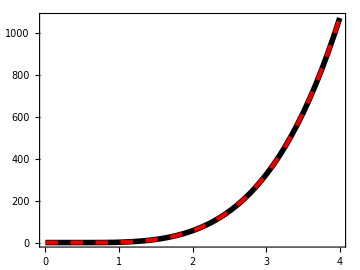

```mathematica
Plot[{PInt[x],PeInt[edInt[x]]},{x,0.001,4}]
```

```mathematica
Max[Table[Abs[PInt[x]-PeInt[edInt[x]]],{x,0.0001,5,.01}]]
```

0.0000132262

```mathematica
dPdE[e_]=(1.2625814949136498*^-42+2.4439030393295734*^-33 e+9.322641344497548*^-26 e^2+1.9540661873302495*^-19 e^3+5.0244280894342345*^-14 e^4+2.369176131226614*^-9 e^5+0.00002467595835925649 e^6+0.0608709022174928 e^7+35.13582886022962 e^8+4222.887394189519 e^9+72483.09074617726 e^10+417317.67297479673 e^11+585334.4710663276 e^12+57539.2198687339 e^13+14441.972045822631 e^14+1216.0067118006687 e^15+13.489236656837132 e^16+14.786577881305382 e^17-2.5565796031645758 e^18+0.05603218920634199 e^19+0.000984102224155054 e^20+2.1161830800816893*^-6 e^21+8.101199742688298*^-10 e^22+3.89552175647867*^-14 e^23)/(3.56558833745313*^-41+4.6403916630291216*^-32 e+1.246926715508643*^-24 e^2+1.9406804331642527*^-18 e^3+3.8792079821435393*^-13 e^4+1.473941085930358*^-8 e^5+0.0001283715493908053 e^6+0.27578987407916083 e^7+144.29417387657588 e^8+16436.520976883963 e^9+315466.19533599314 e^10+2.8901807318940037*^6 e^11+5.506960426273549*^6 e^12-355776.5733809447 e^13+156209.84678369848 e^14-5701.991686556281 e^15+832.8660760210314 e^16+1.9784144986425583 e^17-7.706332342730179 e^18+0.20216864185984038 e^19+0.00313721024057907 e^20+6.541440626577012*^-6 e^21+2.4689937881750025*^-9 e^22+1.1758507795621395*^-13 e^23);
```

```mathematica
Tint[e_]=(-4.873400811469563*^-10-0.33967898165285937 e-243.87315076666465 e^2-7950.4417656525575 e^3-15830.731725359203 e^4-1638.2165592489832 e^5-15.708990537469983 e^6-0.017506852476184522 e^7-1.836593645164133*^-6 e^8)/(-4.873378567876981*^-6-1.9735695129421675 e-691.5144322242182 e^2-13185.130839434429 e^3-20098.669864541644 e^4-1169.8522357611525 e^5-6.630649855145946 e^6-0.004312673981317225 e^7-2.1655522622011757*^-7 e^8);
```

```mathematica
ed[T_]=(-0.011958188410851651+119.89423098138208 T-3156.9475699248055 T^2+32732.86844374939 T^3-187899.8994764422 T^4+712537.3610845465 T^5-1.557049803609345*^6 T^6+1.4852519861308339*^6 T^7+532132.6079941876 T^8-1.963099445042592*^6 T^9-4484.44579242679 T^10+1.7984228830058286*^6 T^11+119345.25619517374 T^12-1.3499773937058165*^6 T^13-207838.4995663606 T^14+654970.2138652403 T^15-78643.00334616247 T^16+40274.00078068926 T^17+422619.58977657766 T^18-409688.07836393174 T^19-62005.75915066359 T^20+46788.14270090656 T^21+40784.330477857235 T^22-12589.47744840392 T^23)/(31630.074365558292-127100.88940643385 T+173528.1225422275 T^2-39403.297956865215 T^3-85582.57873541754 T^4+9320.560804233442 T^5+50882.74198960172 T^6+20335.926473421183 T^7-14897.725710713818 T^8-23836.484117457 T^9-13726.013896090335 T^10+4517.908673107615 T^11+18056.19917986404 T^12+14954.82860467155 T^13+2569.623976952738 T^14-9304.046211514986 T^15-15606.429173842751 T^16+8383.710735812094 T^17+1591.3177623932843 T^18-678.748230997762 T^19-33.58687934953277 T^20+3.2520554133126285 T^21-0.19647288043440464 T^22+0.005443394551264717 T^23);
```

```mathematica
LogPLogEd[Log[10,ed[5]]]
```

3.42773

```mathematica
equilibriumPressure[e_]=LogPLogEd[Log[10,e]];
```

```mathematica
M0=12.473;
M1=0.046;
M2=0.057;
M2=M1^2+M2^2;
f[e_]:=M0-M2/(M0+equilibriumPressure[e])-e
```

```mathematica
Solve[a-b/(a+p/e)-e==0,e]//FullSimplify
```

{{e→(a^2-b-p+√(4 a^2 p+(-a^2+b+p)^2))/(2 a)},{e→-(-a^2+b+p+√(4 a^2 p+(-a^2+b+p)^2))/(2 a)}}

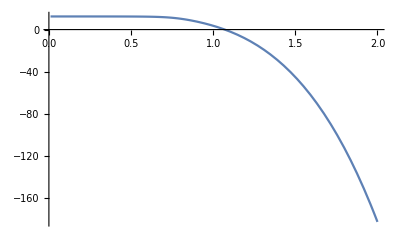

```mathematica
Plot[f[ed[T]],{T,0.01,2}]
```

```mathematica
FindRoot[f[ed[T]]==0,{T,1.5}]
```

{T→1.07079}

```mathematica
.015^2
```

0.000225

```mathematica
D[(a-e)(a+p[e]),e]
```

-a-p[e]+(a-e) p'[e]

```mathematica
{ed[.01],ed[2],ed[5]}
```

{0.0000297011,195.297,8254.11}

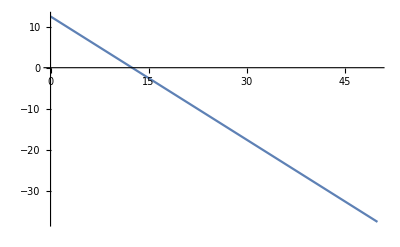

```mathematica
Plot[f[e],{e,0.00002970113634643915,50}]
```

```mathematica
f[M0]*f[0.01]
```

-0.00519789

```mathematica
{f[0.01],f[.001]}
```

{12.4625,12.4714}

```mathematica
D[a-b/(a+p[e])-e,e]
```

-1+(b p'[e])/(a+p[e])^2

```mathematica
df[e_]=-1+M2*dPdE[e]/(M0+equilibriumPressure[e]);
```

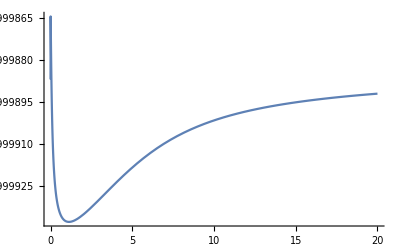

```mathematica
Plot[df[e],{e,0.00002970113634643915,20},PlotRange->All]
```

```mathematica
f[.01]
```

12.4625

```mathematica
f[50]
```

-37.5274

```mathematica
f[M0]
```

-0.000417084

```mathematica
FindRoot[f[e],{e,0.00002970113634643915,8254.108180008152}]
```

{e→12.4726}

```mathematica
ed[1.0707912711150502]
```

12.4726

```mathematica
e1=0.0000297082113634643915;
e2=8254.108180008152;
f1=f[e1];
fmid=f[e2];
If[f1*fmid≥0.0,Print["Root must be bracketed for bisection method"];];
```

```mathematica
M0=-24.248;
M1=-0.103;
M2=-98.384;
M=M1^2+M2^2;
cst2[e_]:=equilibriumPressure[e]/e
func[e_]:=e+(M0*(1-cst2[e])-Sqrt[(M0*(1-cst2[e]))^2+4*cst2[e]*(M0^2-M)])/(2cst2[e])
```

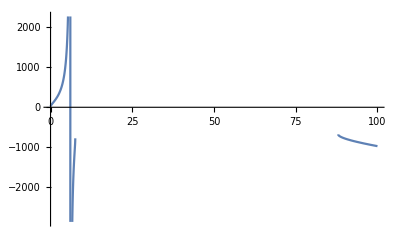

```mathematica
Plot[func[e],{e,0.00002970113634643915,100}]
```

```mathematica
func[40]
```

-435.333-373.616 ⅈ

```mathematica
cst2[40]
```

0.0248719

```mathematica
{M0^2,M}
```

{587.966,9679.42}

## bulk viscosity

```mathematica
Tint[e_]=(1.510073201405604*^-29+8.014062800678687*^-18 e+2.4954778310451065*^-10 e^2+0.000063810382643387 e^3+0.4873490574161924 e^4+207.48582344326206 e^5+6686.07424325115 e^6+14109.766109389702 e^7+1471.6180520527757 e^8+14.055788949565482 e^9+0.015421252394182246 e^10+1.5780479034557783*^-6 e^11)/(7.558667139355393*^-28+1.3686372302041508*^-16 e+2.998130743142826*^-9 e^2+0.0005036835870305458 e^3+2.316902328874072 e^4+578.0778724946719 e^5+11179.193315394154 e^6+17965.67607192861 e^7+1051.0730543534657 e^8+5.916312075925817 e^9+0.003778342768228011 e^10+1.8472801679382593*^-7 e^11);
```

```mathematica
zetabar[e_]:=Module[{A1,A2,A3,lambda1,lambda2,lambda3,lambda4,sigma1,sigma2,sigma3,sigma4,x,res},
A1=-13.77;
A2=27.55;
A3=13.45;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;
x=Tint[e]/1.01355;
If[x>1.05,Return[lambda1*Exp[-(x-1)/sigma1]+lambda2*Exp[-(x-1)/sigma2]+0.001]];
If[x<0.995,Return[lambda3*Exp[(x-1)/sigma3]+lambda4*Exp[(x-1)/sigma4]+0.03]];
If[x==0.995,Return[((lambda3*Exp[(x-1)/sigma3]+lambda4*Exp[(x-1)/sigma4]+0.03)+(A1*x*x+A2*x-A3))/2]];
Return[A1*x*x+A2*x-A3];
];
```

```mathematica
zetabarData=Table[{edInt[T],zetabar[edInt[T]]},{T,0.001,5,.0001}];
```

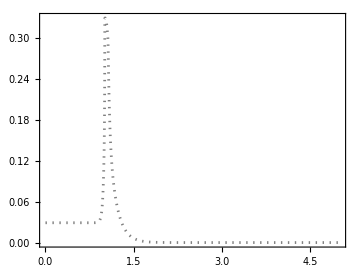

```mathematica
Plot[zetabar[edInt[T]],{T,.001,5}]
```

```mathematica
zetabarDataInt=Interpolation[Table[{T,zetabar[edInt[T]]},{T,0.001,5,.0001}],InterpolationOrder->3]
```

InterpolatingFunction[{{0.001, 5.}}, <>]

```mathematica
data=Table[{T,zetabar[edInt[T]]},{T,0.001,5,.01}];
zetabar2=InterpolatingPolynomial[data,T]
```

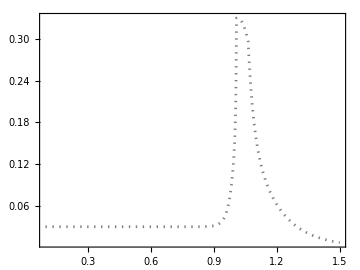

```mathematica
Plot[zetabar[edInt[T]],{T,.1,1.5}]
```

```mathematica
zetabarData=Table[{edInt[T],zetabarDataInt[T]},{T,0.001,5,.01}];
```

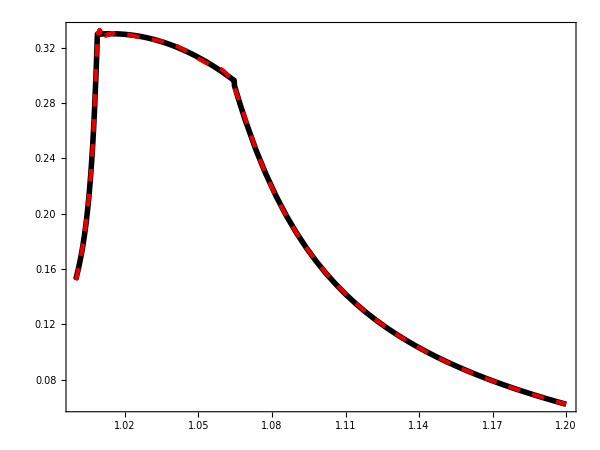

```mathematica
Plot[{zetabarDataInt[T],zetabarInt[edInt[T]]},{T,1,1.2},ImageSize->600]
```

```mathematica
zetabarInt[e_]=rationalPolyFit[zetabarData,13,13]/.{x->e}
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

(4.99747×10^6-3.50423×10^6 e+1.06722×10^6 e^2-184952. e^3+20452.8 e^4-1618.65 e^5+110.497 e^6-7.31745 e^7+0.397223 e^8-0.0134925 e^9+0.000209405 e^10-2.99039×10^-7 e^11-4.69569×10^-9 e^12+8.12923×10^-11 e^13)/(1.66574×10^8-1.16598×10^8 e+3.51653×10^7 e^2-5.84867×10^6 e^3+549599. e^4-21086.9 e^5-1436.41 e^6+266.66 e^7-19.1996 e^8+0.817234 e^9-0.0214308 e^10+0.000356445 e^11-5.3546×10^-6 e^12+8.14372×10^-8 e^13)

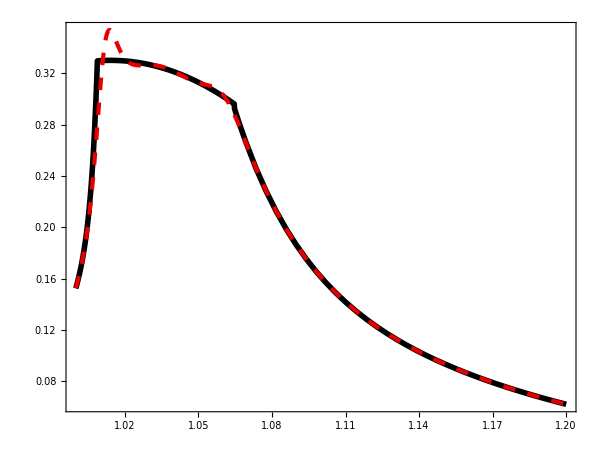

```mathematica
Plot[{zetabar[edInt[T]],zetabarInt[edInt[T]]},{T,1,1.2},ImageSize->600]
```

```mathematica
Max[Table[Abs[zetabar[edInt[T]]-zetabarInt[edInt[T]]],{T,0.001,5,.01}]]
```

0.00148439